```mathematica
m=10;
aspectRatio = 1/2;
```

```mathematica
nullList := Table[Tooltip[{xAxes[[i]],-1}],{i,1,Length[xAxes]}];
```

Read data:

```mathematica
Map[(
Subscript[sigma, #] = Import["C:\\Users\\0wner\\OneDrive - post.bgu.ac.il\\Desktop\\Traffics\\SIGMETRICS traffic\\Traffic "<>ToString[#]<>" for App A sigma.csv","Data"];
)&,{0,0.25,0.5,0.75,1}];
```

Static:

```mathematica
static[kToR_,kAgg_,sigma_]:=Module[{torsAmount,tors,totaltraffic,totalHitAgg},(
torsAmount = Total[Table[(
Sort[sigma[[All,j+1]],Greater][[;;kToR]]
),{j,1,m}],2];
tors = Table[(
SortBy[sigma[[All,{1,j+1}]],-#[[2]]&][[;;kToR,1]]
),{j,1,m}];
totaltraffic =Total[sigma[[All,2;;]],2]; 
totalHitAgg = Total[Sort[Map[(
Total[Table[(
Boole[!MemberQ[tors[[j]],#[[1]]]]*#[[j+1]]
),{j,1,m}]]&
),sigma],Greater][[;;kAgg]]];

{torsAmount/totaltraffic//N,totalHitAgg/totaltraffic//N}
)];
static[200,200,Subscript[sigma, 0.5]]
```

{0.449246,0.06821}

Read file with measure, :

```mathematica
readResult[measure_,alg_,alpha_,kToR_,kAgg_,pAppA_]:=ToExpression[Last[StringSplit[Select[Select[Import["C:\\omnetpp-5.6.1\\samples\\SIGMETRICS24\\simulations\\results\\General-alg="<>ToString[alg]<>",alpha="<>ToString[alpha]<>",kAgg="<>ToString[kAgg]<>",kToR="<>ToString[kToR]<>",probAppA="<>ToString[pAppA]<>"-#0.sca","Data"],#≠{}&],(StringContainsQ[#[[1]],measure])&][[1]][[1]]]]];
```

Figure 1!!

```mathematica
Subscript[sigma, 0.5][[All,2;;]]
```

{{489,1023,1467,1467,739,172,612,1956,1467,978},{2081,0,0,0,0,0,0,0,0,0},{0,0,0,0,3781,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,5452},{7979,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,4915},{489,1359,1337,380,489,329,489,592,895,978},{0,0,0,10042,0,0,0,0,0,0},{978,489,489,1467,489,1262,1158,46,0,787},{0,0,0,0,0,0,0,2014,0,0}}

```mathematica
tally = SortBy[Map[{#[[1]],Total[#[[2]]]}&,Subscript[sigma, 0.5]],(-#[[2]]&)]
mapTag = Transpose[{map[[All,1]],Range[map//Length],N[1/Total[Subscript[sigma, 0.5][[All,2]],2]*map[[All,2]]]}]
```

{{17733,29750},{634139,29750},{6020756,21657},{891084,21470},{4137651,21470},{5569716,21470},{9869617,21120},{4572858,19218},{6053809,17028},{487618,16246},{3343383,15912},{1895593,15870},{3495244,15870},36663,{9996577,0},{9996925,0},{9997257,0},{9997386,0},{9997509,0},{9997634,0},{9997864,0},{9998109,0},{9998302,0},{9998575,0},{9998927,0},{9998949,0},{9999882,0}}
 |  |  |  |

{{17733,1,0.00945924},{255847,2,0.00945924},{634139,3,0.00945924},{1210888,4,0.00945924},{3798982,5,0.00945924},36679,{9929456,36685,3.17958×10^-7},{9933227,36686,3.17958×10^-7},{9945787,36687,3.17958×10^-7},{9957544,36688,3.17958×10^-7},{9996577,36689,3.17958×10^-7}}
 |  |  |  |

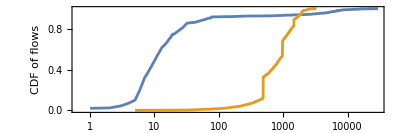

```mathematica
tallyA = Select[Select[SortBy[Map[{#[[1]],Total[#[[2]]]}&,Subscript[sigma, 0.5]],(#[[2]]&)],(#[[2]]>0)&],(#[[1]]>2000)&];
tallyA = Tally[tallyA[[All,2]]];
flowSizesA = tallyA[[All,1]];

tallyB= Select[Select[SortBy[Map[{#[[1]],Total[#[[2]]]}&,Subscript[sigma, 0.5]],(#[[2]]&)],(#[[2]]>0)&],(#[[1]]≤ 2000)&];
tallyB = Tally[tallyB[[All,2]]];
flowSizesB = tallyB[[All,1]];

cdfFlows = ListLogLinearPlot[{Transpose[{flowSizesA,1/Total[tallyA[[All,2]]]*Accumulate[tallyA[[All,2]]]}],Transpose[{flowSizesB,1/Total[tallyB[[All,2]]]*Accumulate[tallyB[[All,2]]]}]},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"Flow size(bytes)","CDF of flows"},GridLines->Automatic,AspectRatio->1/3,PlotLegends->Placed[{"App A","App B"},Above] ]
```

```mathematica
Export["cdfFlows.pdf",cdfFlows]
```

cdfFlows.pdf

Per source:

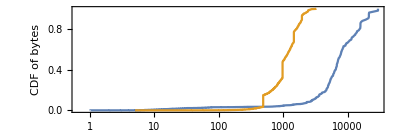

```mathematica
tallyA = Select[Select[SortBy[Map[{#[[1]],Total[#[[2]]]}&,Subscript[sigma, 0.5]],(#[[2]]&)],(#[[2]]>0)&],(#[[1]]>2000)&];
Tally[tallyA[[All,2]]];
trafficLengthA = Total[tallyA[[All,2]]];
flowSizesA = DeleteCases[tallyA[[All,2]],0];

tallyB = Select[Select[SortBy[Map[{#[[1]],Total[#[[2]]]}&,Subscript[sigma, 0.5]],(#[[2]]&)],(#[[2]]>0)&],(#[[1]]≤ 2000)&];
trafficLengthB = Total[tallyB[[All,2]]];
flowSizesB = DeleteCases[tallyB[[All,2]],0];

cdfBytes = ListLogLinearPlot[{Transpose[{flowSizesA,1/trafficLengthA*Accumulate[tallyA[[All,2]]]}],Transpose[{flowSizesB,1/trafficLengthB*Accumulate[tallyB[[All,2]]]}]},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"Flow size(bytes)","CDF of bytes"},GridLines->Automatic,AspectRatio->1/3]
```

```mathematica
Export["cdfBytes.pdf",cdfBytes]
```

cdfBytes.pdf

Per All sources:

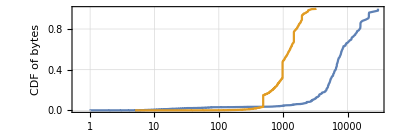

{{1,1/3486},{1,1/1743},{1,1/1162},{1,2/1743},{1,5/3486},{1,1/581},{1,1/498},{1,4/1743},{1,3/1162},{1,5/1743},{1,11/3486},{1,2/581},{1,13/3486},{1,1/249},{1,5/1162},{1,8/1743},{1,17/3486},{1,3/581},3451,{15298,1735/1743},{15758,1157/1162},{15802,248/249},{15870,3473/3486},{15870,579/581},{15870,3475/3486},{15912,1738/1743},{16246,1159/1162},{17028,1739/1743},{19218,497/498},{21120,580/581},{21470,3481/3486},{21470,1741/1743},{21470,1161/1162},{21657,1742/1743},{29750,3485/3486},{29750,1}}
 |  |  |  |

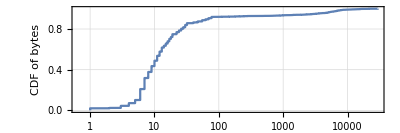

```mathematica
tallyA = Select[Select[SortBy[Map[{#[[1]],Total[#[[2]]]}&,Subscript[sigma, 0.5]],(#[[2]]&)],(#[[2]]>0)&],(#[[1]]>2000)&];
trafficLengthA = Total[tallyA[[All,2]]];
flowSizesA = DeleteCases[tallyA[[All,2]],0];

tallyB = Select[Select[SortBy[Map[{#[[1]],Total[#[[2]]]}&,Subscript[sigma, 0.5]],(#[[2]]&)],(#[[2]]>0)&],(#[[1]]≤ 2000)&];
trafficLengthB = Total[tallyB[[All,2]]];
flowSizesB = DeleteCases[tallyB[[All,2]],0];

pTraffic = ListLogLinearPlot[{Transpose[{flowSizesA,1/trafficLengthA*Accumulate[tallyA[[All,2]]]}],Transpose[{flowSizesB,1/trafficLengthB*Accumulate[tallyB[[All,2]]]}]},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"Flow size(bytes)","CDF of bytes"},PlotLegends->{"App A","App B"},GridLines->Automatic,AspectRatio->1/3]

lA=1/Length[flowSizesA];
lB =1/Length[flowSizesB];
Table[{flowSizesA[[i]],lA*i},{i,1,Length[flowSizesA]}]
Table[{flowSizesB[[i]],lB*i},{i,1,Length[flowSizesB]}];
ListLogLinearPlot[{Table[{flowSizesA[[i]],lA*i},{i,1,Length[flowSizesA]}]},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"Flow size(bytes)","CDF of bytes"},PlotLegends->{"App A","App B"},GridLines->Automatic,AspectRatio->1/3,LabelStyle->Directive[Black,Medium,FontFamily->"Times New Roman"]]
```

```mathematica
flowSizesA//Tally
```

{{1,70},{2,13},{3,71},{4,93},{5,107},{6,375},{7,379},{8,208},{9,201},{10,185},{11,167},{12,144},{13,139},{14,62},{15,75},{16,78},{17,83},{18,64},{19,96},{20,1},{22,70},{24,57},{26,61},{28,51},{30,76},{32,63},{40,25},{42,1},{47,33},{48,1},{55,42},{62,30},{69,39},{74,1},{77,42},{83,1},{86,1},{101,1},{110,4},{143,4},{177,1},{178,4},{181,1},{190,1},{211,3},{245,6},{277,4},{331,1},{398,1},{482,1},{501,1},{519,1},{615,1},{641,1},{674,1},{700,1},{703,1},{710,1},{755,1},{762,1},{774,1},{785,1},{882,3},{919,1},{921,1},{969,1},{987,1},{1003,4},{1029,1},{1030,1},{1088,1},{1126,1},{1284,1},{1303,1},{1364,1},{1371,1},{1373,1},{1441,4},{1557,1},{1577,1},{1582,1},{1881,2},{2007,1},{2019,1},{2081,1},{2088,1},{2147,1},{2224,1},{2287,1},{2289,1},{2321,3},{2322,1},{2333,1},{2573,1},{2623,1},{2699,1},{2716,1},{2727,1},{2761,4},{2859,1},{2861,1},{2871,1},{2920,1},{2934,1},{3033,1},{3078,1},{3132,1},{3153,1},{3201,3},{3268,1},{3281,1},{3287,1},{3308,1},{3453,1},{3491,1},{3505,1},{3532,1},{3582,1},{3633,5},{3646,1},{3697,1},{3770,1},{3908,1},{3954,1},{3974,1},{3996,1},{3999,1},{4066,1},{4253,1},{4414,1},{4458,1},{4538,1},{4540,1},{4561,1},{4632,1},{4683,1},{4706,2},{4722,1},{4724,1},{4772,1},{4779,1},{4851,1},{4909,1},{4935,1},{4957,1},{4968,1},{4973,1},{4974,1},{4990,1},{5013,1},{5089,1},{5094,1},{5100,1},{5114,1},{5158,1},{5160,1},{5227,1},{5258,1},{5272,1},{5318,1},{5332,1},{5344,1},{5364,1},{5400,1},{5408,1},{5419,1},{5422,1},{5485,1},{5491,1},{5556,1},{5590,1},{5626,1},{5653,1},{5672,1},{5768,1},{5794,1},{5941,1},{5951,1},{5984,1},{5994,1},{5995,1},{6038,1},{6115,1},{6171,1},{6185,1},{6212,1},{6222,1},{6279,1},{6290,1},{6384,1},{6400,1},{6558,1},{6579,1},{6609,1},{6624,1},{6636,1},{6642,1},{6725,1},{6745,1},{6808,1},{6820,4},{6860,1},{6926,1},{6928,1},{6998,1},{7018,1},{7054,1},{7081,1},{7099,1},{7120,1},{7150,1},{7200,1},{7252,1},{7255,1},{7354,1},{7492,1},{7568,1},{7586,1},{7665,1},{7719,1},{7790,1},{7860,1},{7875,1},{7898,1},{7978,1},{7979,1},{7984,1},{8114,1},{8141,1},{8196,1},{8287,1},{8390,1},{8410,1},{8489,1},{8604,1},{8614,1},{8649,1},{9264,1},{9319,1},{9357,1},{9584,1},{9612,1},{10140,1},{10318,1},{10611,1},{10763,1},{11422,1},{11511,1},{11580,1},{11719,1},{12320,1},{12525,1},{13160,1},{13222,1},{13640,1},{13986,1},{14047,1},{14944,1},{15298,1},{15758,1},{15802,1},{15870,3},{15912,1},{16246,1},{17028,1},{19218,1},{21120,1},{21470,3},{21657,1},{29750,2}}

```mathematica
Export["TrafficCDFFigure2.pdf",pTraffic]
```

TrafficCDFFigure2.pdf

```mathematica
legend = LineLegend[ColorData[97,"ColorList"],{"Insertion cost","Controller","ToR","Aggregation"},LegendMarkers->"OpenMarkers",LegendLayout->{"Column",2}]
Export["lables.pdf",legend]
```

lables.pdf

Figure 2 !!!!

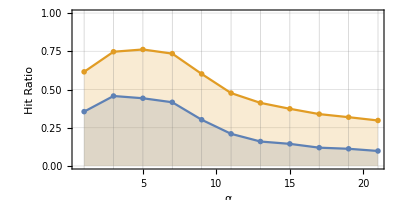
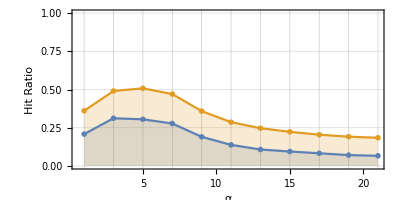
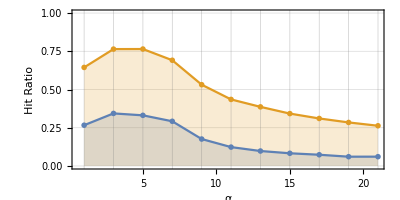
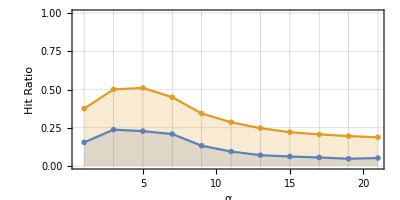
((150
750) | (75
375)
(110
1100) | (55
550)) | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
measureToR = "Hit_ratio_ToR";
measureToRAgg = "Hit_ratio_Agg_from_all_traffic";
alphas = Range[1,21,2];
kToR = 150;
kAgg = 750;
pAlg = 0.5;
alg = 5;
p11 = ListLinePlot[{Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]+readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α","Hit Ratio"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ];

pAlg = 0.5;
alg = 5;
kToR = 75;
kAgg = 375;
p22 = ListLinePlot[{Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]+readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α","Hit Ratio"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ];
pAlg = 0.5;
alg = 5;
kToR = 110;
kAgg = 1100;
p33 = ListLinePlot[{Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]+readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α","Hit Ratio"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ];

pAlg = 0.5;
alg = 5;
kToR = 55;
kAgg = 550;
p44 = ListLinePlot[{Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]+readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α","Hit Ratio"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ];
Grid[{{MatrixForm[{{{150,750},{75,375}},{{110,1100},{55,550}}}]},{p11,p22},{p33,p44}}]
```

Export the file:

```mathematica
Export["SIGMETRICS PLOTS//Fig2 1.pdf",p11]
Export["SIGMETRICS PLOTS//Fig2 2.pdf",p22]
Export["SIGMETRICS PLOTS//Fig2 3.pdf",p33]
Export["SIGMETRICS PLOTS//Fig2 4.pdf",p44]
```

SIGMETRICS PLOTS//Fig2 1.pdf

SIGMETRICS PLOTS//Fig2 2.pdf

SIGMETRICS PLOTS//Fig2 3.pdf

SIGMETRICS PLOTS//Fig2 4.pdf

Figure3:

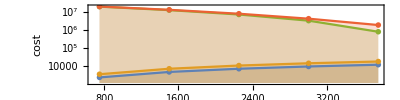

```mathematica
plotHitRatioFig3[input_]:=ListLinePlot[input,PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},Ticks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio,PlotLegends->{"Hit Ration in ToRs","Hit Ratio in Agg"}];

plotInsertionCountFig3[input_]:=ListLogPlot[input,PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},Ticks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","insertion_count"},Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,2 10^7}},Joined->True];ListLogPlot[Map[Tooltip[Transpose[{xAxes,#}]]&,Transpose[Table[Accumulate[{α*m*torSizesLables[[i]],α*aggs[[i]],trafficLength*(1 -staticFig2[[i]][[1]]-  staticFig2[[i]][[1]]),ϵ*trafficLength* staticFig2[[i]][[2]]}],{i,1,Length[xAxes]}]]],PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},Ticks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","cost"},Frame->True,AspectRatio->aspectRatio,Joined->True]
```

```mathematica
aggs = {250,500,750,1000,1250};
torSizes = {50,100,150,200,250};


staticFig2= Map[static[#[[1]],#[[2]],Subscript[sigma, 0.5]]&,Transpose[{torSizes,aggs}]]
```

{{0.199019,0.0848512},{0.30631,0.159306},{0.388752,0.228006},{0.449246,0.28982},{0.48776,0.335638}}

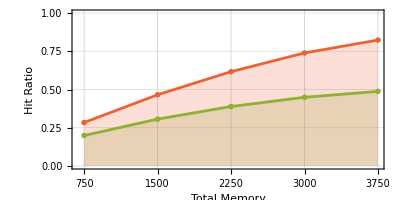
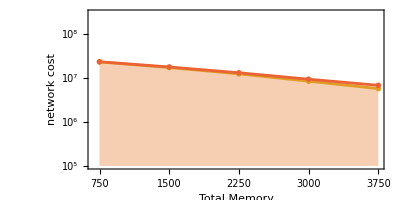
-Graphics- | -Graphics3D- | -Graphics-

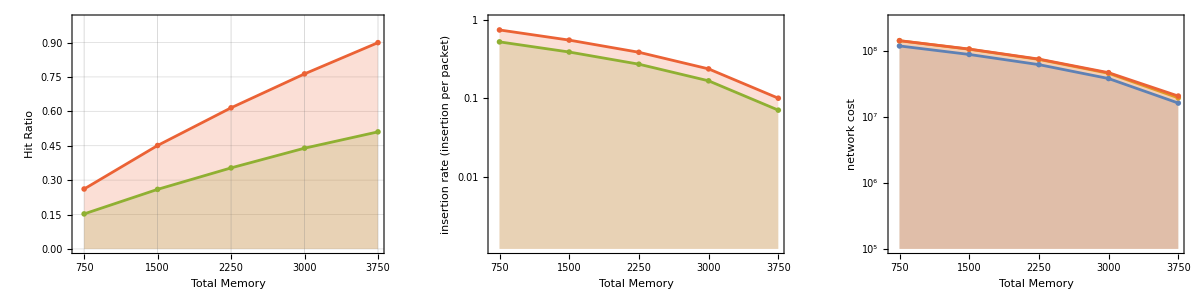

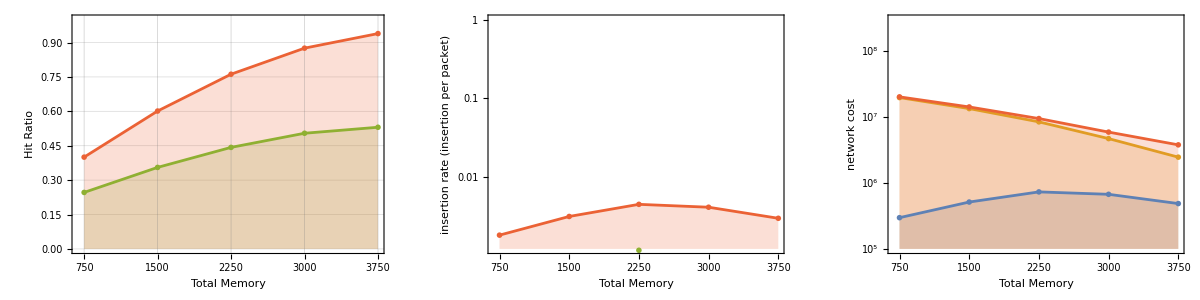

```mathematica
aggs = {250,500,750,1000,1250};
torSizes = {50,100,150,200,250};
xAxes = 10*torSizes+aggs;
torSizesLables = torSizes;
ϵ = 0.1;
trafficLength = Total[Subscript[sigma, 0.5][[All,2;;]],2];
α = 5;
rangeToCost = {10^5,3 10^8};
rangeInsertion = {0,1};
p1=Grid[{{ ListLinePlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]], staticFig2[[i]][[1]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]], staticFig2[[i]][[1]]+ staticFig2[[i]][[2]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio ],-Graphics3D-,
ListLogPlot[{Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])+trafficLength*(1 -staticFig2[[i]][[1]]-  staticFig2[[i]][[2]])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])+trafficLength*(1 -staticFig2[[i]][[1]]-  staticFig2[[i]][[2]])+ϵ*trafficLength*staticFig2[[i]][[2]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,{10^5,10^6,10^7,10^8}},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,rangeToCost} ]
}}]

i=1;
Subscript[α, naine] = 5;
alg = 1;
j=1;
pAlg = 0.5;

pAlgs = 0.5;


p2=Grid[{{ListLinePlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,Subscript[α, naine] ,torSizesLables[[i]],aggs[[i]],0.5]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,Subscript[α, naine] ,torSizesLables[[i]],aggs[[i]],0.5]+readResult["Hit_ratio_Agg_from_all_traffic",alg,Subscript[α, naine] ,torSizesLables[[i]],aggs[[i]],0.5]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio ],ListLogPlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],1/trafficLength*readResult["insertion_count_ToR",alg,Subscript[α, naine],torSizesLables[[i]],aggs[[i]],0.5]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],1/trafficLength*(readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],0.5]+readResult["insertion_count_Agg",alg,Subscript[α, naine],torSizesLables[[i]],aggs[[i]],0.5])}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","insertion rate\n(insertion per packet)"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,rangeInsertion} ],ListLogPlot[{Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+α*readResult["insertion_count_Agg",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+α*readResult["insertion_count_Agg",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+trafficLength*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]- readResult["Hit_ratio_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+α*readResult["insertion_count_Agg",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+trafficLength*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]- readResult["Hit_ratio_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg])+ϵ*trafficLength*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->rangeToCost ]}}]
alg = 5;
p3=Grid[{{ListLinePlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,α,torSizesLables[[i]],aggs[[i]],0.5]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,α,torSizesLables[[i]],aggs[[i]],0.5]+readResult["Hit_ratio_Agg_from_all_traffic",alg,α,torSizesLables[[i]],aggs[[i]],0.5]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio ],ListLogPlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],1/trafficLength*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],0.5]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],1/trafficLength*(readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],0.5]+readResult["insertion_count_Agg",alg,α,torSizesLables[[i]],aggs[[i]],0.5])}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","insertion rate\n(insertion per packet)"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,rangeInsertion} ],ListLogPlot[{Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+α*readResult["insertion_count_Agg",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+α*readResult["insertion_count_Agg",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+trafficLength*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]- readResult["Hit_ratio_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+α*readResult["insertion_count_Agg",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]+trafficLength*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]- readResult["Hit_ratio_ToR",alg,α,torSizesLables[[i]],aggs[[i]],pAlg])+ϵ*trafficLength*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,torSizesLables[[i]],aggs[[i]],pAlg]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->rangeToCost ]}}]
```

```mathematica
Table[Tooltip[{xAxes[[i]],1/trafficLength*readResult["insertion_count_ToR",alg,α,torSizesLables[[i]],aggs[[i]],0.5]}],{i,1,Length[xAxes]}]//N
```

{{750.,0.000625635},{1500.,0.000970408},{2250.,0.00118229},{3000.,0.00096741},{3750.,0.000998377}}

Export to pdf:

```mathematica
Export["Fig3HitRatioStat.pdf",p1[[1]][[1]][[1]]]
Export["Fig3insertionStat.pdf",p1[[1]][[1]][[2]]]
Export["Fig3HitCostStat.pdf",p1[[1]][[1]][[3]]]

Export["Fig3HitRatioNaive.pdf",p2[[1]][[1]][[1]]]
Export["Fig3insertionNaive.pdf",p2[[1]][[1]][[2]]]
Export["Fig3HitCostNaive.pdf",p2[[1]][[1]][[3]]]

Export["Fig3HitRatioIVanilla.pdf",p3[[1]][[1]][[1]]]
Export["Fig3insertionIVanilla.pdf",p3[[1]][[1]][[2]]]
Export["Fig3HitCostIVanilla.pdf",p3[[1]][[1]][[3]]]
```

Fig3HitRatioStat.pdf

Fig3insertionStat.pdf

Fig3HitCostStat.pdf

Fig3HitRatioNaive.pdf

Fig3insertionNaive.pdf

Fig3HitCostNaive.pdf

Fig3HitRatioIVanilla.pdf

Fig3insertionIVanilla.pdf

Fig3HitCostIVanilla.pdf

```mathematica
lable = PointLegend[97,{1,2},LegendMarkers->"OpenMarkers"][[4]]
```

```mathematica
Export["lables.pdf",lable]
```

lables.pdf

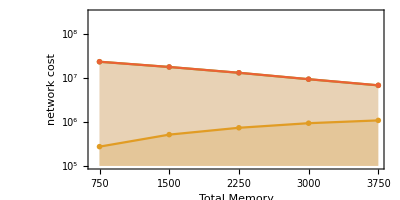

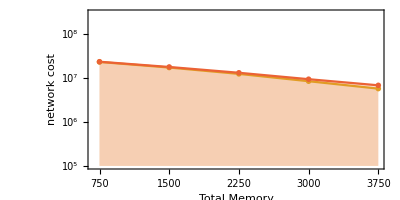

```mathematica
ListLogPlot[{Table[Tooltip[{xAxes[[i]],-1}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength*staticFig2[[i]][[2]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength*staticFig2[[i]][[2]]+trafficLength*(1 -staticFig2[[i]][[1]]-  staticFig2[[i]][[2]])}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength*staticFig2[[i]][[2]]+trafficLength*(1 -staticFig2[[i]][[1]]-  staticFig2[[i]][[2]])+α*(aggs[[i]]+10*torSizesLables[[i]])}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,{10^5,10^6,10^7,10^8}},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,rangeToCost} ]

ListLogPlot[{Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])+trafficLength*(1 -staticFig2[[i]][[1]]-  staticFig2[[i]][[2]])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])+trafficLength*(1 -staticFig2[[i]][[1]]-  staticFig2[[i]][[2]])+ϵ*trafficLength*staticFig2[[i]][[2]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,{10^5,10^6,10^7,10^8}},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memory","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,rangeToCost} ]
```

Figure 3:

```mathematica
xAxes = {0,0.25,0.5,0.75,1};
staticFig3= Map[static[150,750,Subscript[sigma, #]]&,xAxes]
```

{{0.159901,0.371818},{0.270471,0.315968},{0.388752,0.228006},{0.463049,0.131221},{0.503546,0.142362}}

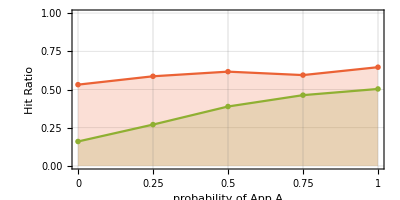
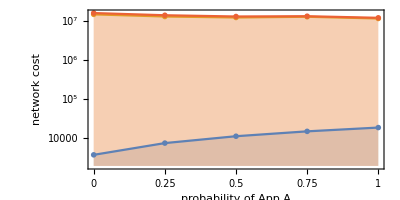
-Graphics- | -Graphics3D- | -Graphics-

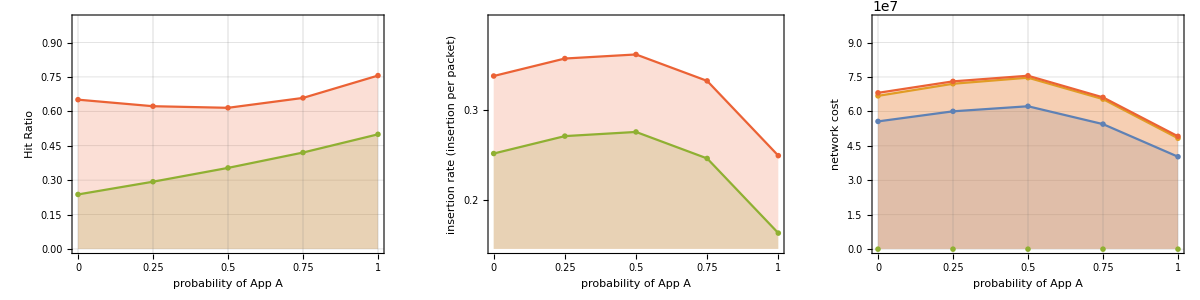

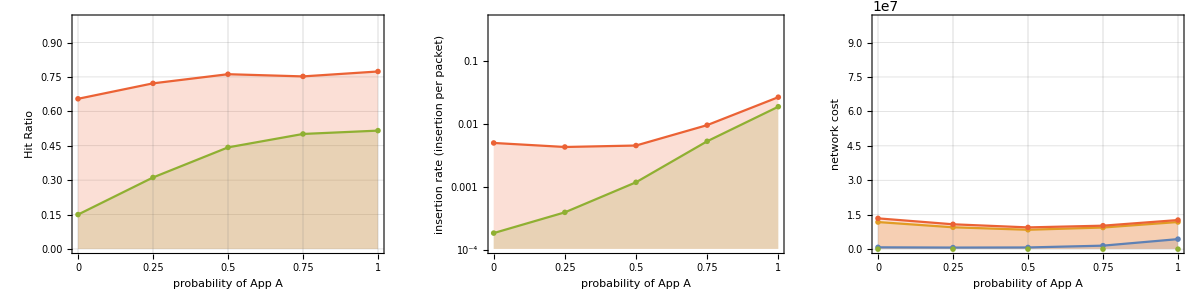

```mathematica
ϵ = 1/10;
xAxes = {0,0.25,0.5,0.75,1};
trafficLength = Map[Total[Subscript[sigma, #][[All,2;;]],2]&,xAxes];
α = 5;
rangeToCost = {10^5,10^8};
rangeInsertion = {0,0.45};
p1=Grid[{{ ListLinePlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]], staticFig3[[i]][[1]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]], staticFig3[[i]][[1]]+ staticFig3[[i]][[2]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio ],-Graphics3D-,
ListLogPlot[{Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])+trafficLength[[i]]*(1 -staticFig3[[i]][[1]]-  staticFig3[[i]][[2]])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*(aggs[[i]]+10*torSizesLables[[i]])+trafficLength[[i]]*(1 -staticFig3[[i]][[1]]-  staticFig3[[i]][[2]])+ϵ*trafficLength[[i]]*staticFig3[[i]][[2]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,{10^5,10^6,10^7,10^8}},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,All} ]
}}]

i=1;
Subscript[α, naine] = 5;
alg = 1;
j=1;

pAlgs = xAxes;
kAgg = 750;
kToR = 150;

p2=Grid[{{ListLinePlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,Subscript[α, naine] ,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,Subscript[α, naine] ,kToR,kAgg,pAlgs[[i]]]+readResult["Hit_ratio_Agg_from_all_traffic",alg,Subscript[α, naine] ,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio ],ListLogPlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],1/trafficLength[[i]]*readResult["insertion_count_ToR",alg,Subscript[α, naine],kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],1/trafficLength[[i]]*(readResult["insertion_count_ToR",alg,Subscript[α, naine],kToR,kAgg,pAlgs[[i]]]+readResult["insertion_count_Agg",alg,Subscript[α, naine],kToR,kAgg,pAlgs[[i]]])}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","insertion rate\n(insertion per packet)"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,rangeInsertion} ],ListLinePlot[{Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])+ϵ*trafficLength[[i]]*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->rangeToCost ]}}]
alg = 5;
p3=Grid[{{ListLinePlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio ],ListLogPlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],1/trafficLength[[i]]*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],1/trafficLength[[i]]*(readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]])}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","insertion rate\n(insertion per packet)"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,rangeInsertion} ],ListLinePlot[{Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])+ϵ*trafficLength[[i]]*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->rangeToCost ]}}]
```

Export to pdf:

```mathematica
Export["SIGMETRICS PLOTS//Fig5HitRatioStat.pdf",p1[[1]][[1]][[1]]]
Export["SIGMETRICS PLOTS//Fig5insertionStat.pdf",p1[[1]][[1]][[2]]]
Export["SIGMETRICS PLOTS//Fig5HitCostStat.pdf",p1[[1]][[1]][[3]]]

Export["SIGMETRICS PLOTS//Fig5HitRatioNaive.pdf",p2[[1]][[1]][[1]]]
Export["SIGMETRICS PLOTS//Fig5insertionNaive.pdf",p2[[1]][[1]][[2]]]
Export["SIGMETRICS PLOTS//Fig5HitCostNaive.pdf",p2[[1]][[1]][[3]]]

Export["SIGMETRICS PLOTS//Fig5HitRatioIVanilla.pdf",p3[[1]][[1]][[1]]]
Export["SIGMETRICS PLOTS//Fig5insertionIVanilla.pdf",p3[[1]][[1]][[2]]]
Export["SIGMETRICS PLOTS//Fig5HitCostIVanilla.pdf",p3[[1]][[1]][[3]]]
```

SIGMETRICS PLOTS//Fig5HitRatioStat.pdf

SIGMETRICS PLOTS//Fig5insertionStat.pdf

SIGMETRICS PLOTS//Fig5HitCostStat.pdf

SIGMETRICS PLOTS//Fig5HitRatioNaive.pdf

SIGMETRICS PLOTS//Fig5insertionNaive.pdf

SIGMETRICS PLOTS//Fig5HitCostNaive.pdf

SIGMETRICS PLOTS//Fig5HitRatioIVanilla.pdf

SIGMETRICS PLOTS//Fig5insertionIVanilla.pdf

SIGMETRICS PLOTS//Fig5HitCostIVanilla.pdf

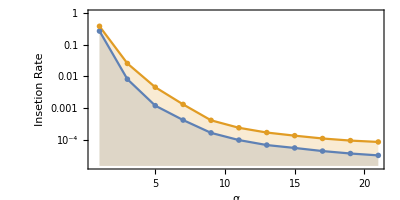
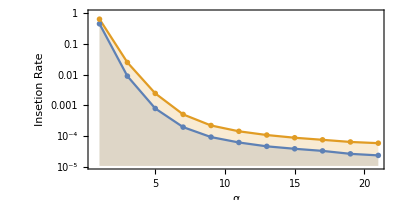
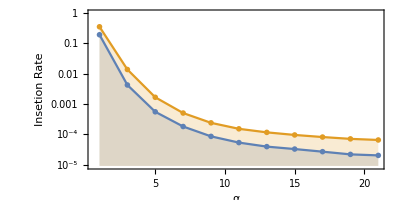
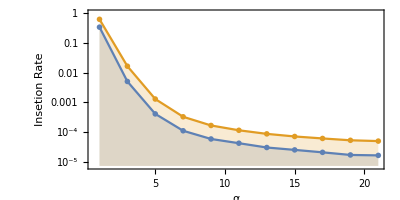
((150
750) | (75
375)
(110
1100) | (55
550)) | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
measureToR = "insertion_count_ToR";
measureToRAgg = "insertion_count_Agg";
normaltraceLen = 1/Total[Subscript[sigma, 0.5][[All,2;;]],2];
yAxesLabel = "Insetion Rate";
alphas = Range[1,21,2];
kToR = 150;
kAgg = 750;
pAlg = 0.5;
alg = 5;
p11 = ListLogPlot[{Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]+normaltraceLen*readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α",yAxesLabel} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ,Joined->True];

pAlg = 0.5;
alg = 5;
kToR = 75;
kAgg = 375;
p22 = ListLogPlot[{Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]+normaltraceLen*readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α",yAxesLabel} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ,Joined->True];
pAlg = 0.5;
alg = 5;
kToR = 110;
kAgg = 1100;
p33 = ListLogPlot[{Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]+normaltraceLen*readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α",yAxesLabel} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ,Joined->True];

pAlg = 0.5;
alg = 5;
kToR = 55;
kAgg = 550;
p44 = ListLogPlot[{Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,normaltraceLen*readResult[measureToR,alg,#,kToR,kAgg,pAlg]+normaltraceLen*readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α",yAxesLabel} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}} ,Joined->True];
Grid[{{MatrixForm[{{{150,750},{75,375}},{{110,1100},{55,550}}}]},{p11,p22},{p33,p44}}]
```

Export the file:

```mathematica
Export["SIGMETRICS PLOTS//Fig2 1 insertion count.pdf",p11]
Export["SIGMETRICS PLOTS//Fig2 2 insertion count.pdf.pdf",p22]
Export["SIGMETRICS PLOTS//Fig2 3 insertion count.pdf.pdf",p33]
Export["SIGMETRICS PLOTS//Fig2 4 insertion count.pdf.pdf",p44]
```

SIGMETRICS PLOTS//Fig2 1 insertion count.pdf

SIGMETRICS PLOTS//Fig2 2 insertion count.pdf.pdf

SIGMETRICS PLOTS//Fig2 3 insertion count.pdf.pdf

SIGMETRICS PLOTS//Fig2 4 insertion count.pdf.pdf

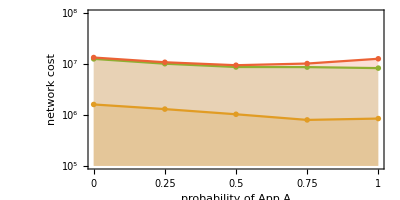

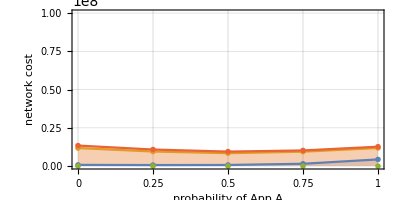

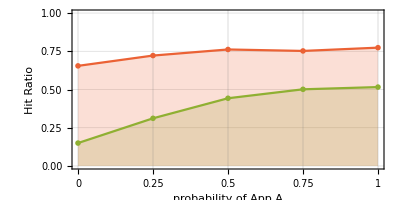

```mathematica
alg=5;
ListLogPlot[{Table[Tooltip[{xAxes[[i]],-1}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength[[i]]*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength[[i]]*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength[[i]]*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])+α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->rangeToCost ]



ListLinePlot[{Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])}],{i,1,Length[xAxes]}],nullList,Table[Tooltip[{xAxes[[i]],α*readResult["insertion_count_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+α*readResult["insertion_count_Agg",alg,α,kToR,kAgg,pAlgs[[i]]]+trafficLength[[i]]*(1 -readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]- readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]])+ϵ*trafficLength[[i]]*readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->rangeToCost ]


ListLinePlot[{nullList,nullList,Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],readResult["Hit_ratio_ToR",alg,α,kToR,kAgg,pAlgs[[i]]]+readResult["Hit_ratio_Agg_from_all_traffic",alg,α,kToR,kAgg,pAlgs[[i]]]}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","Hit Ratio"},Frame->True,PlotRange->{All,{0,1}},AspectRatio->aspectRatio ]
```

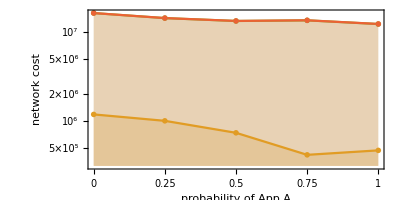

-Graphics-

```mathematica
ListLogPlot[{Table[Tooltip[{xAxes[[i]],-1}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength[[i]]*staticFig3[[i]][[2]]}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength[[i]]*staticFig3[[i]][[2]]+trafficLength[[i]]*(1 -staticFig3[[i]][[1]]-  staticFig3[[i]][[2]])}],{i,1,Length[xAxes]}],Table[Tooltip[{xAxes[[i]],ϵ*trafficLength[[i]]*staticFig3[[i]][[2]]+trafficLength[[i]]*(1 -staticFig3[[i]][[1]]-  staticFig3[[i]][[2]])+α*(aggs[[i]]+10*torSizesLables[[i]])}],{i,1,Length[xAxes]}]},PlotMarkers->"OpenMarkers",GridLines->{xAxes,{10^5,10^6,10^7,10^8}},FrameTicks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"probability of App A","network cost"},Frame->True,AspectRatio->aspectRatio,Joined->True,PlotRange->{All,All} ]
```

```mathematica
1/2
```

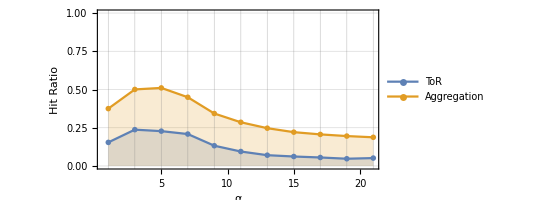

```mathematica
legend=LineLegend[colors,legendLabels,LegendMarkers->markers,LegendMarkerSize->20,LegendLayout->"Row"];
legend = {"ToR","Aggregation"};
figure2WithLable = ListLinePlot[{Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]}]&,alphas],Map[Tooltip[{#,readResult[measureToR,alg,#,kToR,kAgg,pAlg]+readResult[measureToRAgg,alg,#,kToR,kAgg,pAlg]}]&,alphas]},PlotMarkers->"OpenMarkers",GridLines->{alphas,Automatic},Ticks->{alphas[[;;;;3]],Automatic},Filling->Axis,FrameLabel->{"α","Hit Ratio"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}},PlotLegends-> Placed[legend,{Right,Top}],LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"]]
```

```mathematica
Export["figure2WithLable.pdf",figure2WithLable]
```

figure2WithLable.pdf

Compare to results with Nvidia:

```mathematica
convertAggToToRLable[x_]:=ToString[x]<>"#2f5";
```

```mathematica
xAxes = {0,0.25,0.5,0.75,1};
kAgg = 750;
kToR = 150;
staticFig3= Map[static[kToR,kAgg,Subscript[sigma, #]]&,xAxes]
```

{{0.159901,0.371818},{0.270471,0.315968},{0.388752,0.228006},{0.463049,0.131221},{0.503546,0.142362}}

```mathematica
alg = 1;
α=5;
pAlgs = xAxes;
dataHitRatio = Map[Table[{xAxes[[i]],readResult["Total Hit Ratio",#,α,kToR,kAgg,pAlgs[[i]]]},{i,1,Length[xAxes]}]&,{1,6,5}]~Join~{Table[{xAxes[[i]],Total[staticFig3[[i]]]},{i,1,Length[xAxes]}]};
dataInsertionRate = Map[Table[{xAxes[[i]],readResult["Total insertion rate",#,α,kToR,kAgg,pAlgs[[i]]]},{i,1,Length[xAxes]}]&,{1,6,5}]
```

{{{0,0.349212},{0.25,0.377755},{0.5,0.384724},{0.75,0.341623},{1,0.244143}},{{0,0.405421},{0.25,0.302753},{0.5,0.212894},{0.75,0.139132},{1,0.0677559}},{{0,0.00492967},{0.25,0.00430507},{0.5,0.00451178},{0.75,0.00951312},{1,0.0264277}}}

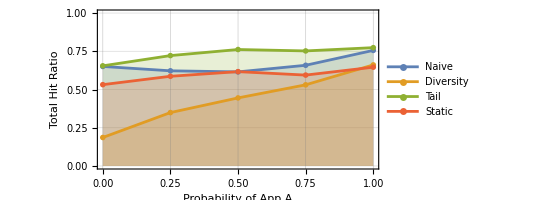

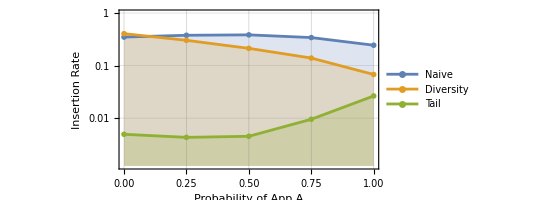

```mathematica
xAxes = {0,0.25,0.5,0.75,1};
ListLinePlot[dataHitRatio,PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},Ticks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Probability of App A","Total Hit Ratio"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}},PlotLegends->{"Naive","Diversity","Tail","Static"},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"]]

ListLogPlot[dataInsertionRate,PlotMarkers->"OpenMarkers",GridLines->{xAxes,Automatic},Ticks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Probability of App A","Insertion Rate"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}},PlotLegends->{"Naive","Diversity","Tail"},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],Joined->True]
```

```mathematica
xAxes = {250,500,750,1000,1250};
staticFig4= Map[static[#/5,#,Subscript[sigma, 0.5]]&,xAxes]
```

{{0.199019,0.0848512},{0.30631,0.159306},{0.388752,0.228006},{0.449246,0.28982},{0.48776,0.335638}}

```mathematica
α=5;
dataHitRatio2 = Map[Table[{3*xAxes[[i]],readResult["Total Hit Ratio",#,α,convertAggToToRLable[xAxes[[i]]],xAxes[[i]],0.5]},{i,1,Length[xAxes]}]&,{1,6,5}]~Join~{Table[{3*xAxes[[i]],Total[staticFig4[[i]]]},{i,1,Length[xAxes]}]};
dataInsertionRate2 = Map[Table[{3*xAxes[[i]],readResult["Total insertion rate",#,α,convertAggToToRLable[xAxes[[i]]],xAxes[[i]],0.5]},{i,1,Length[xAxes]}]&,{1,6,5}]
```

{{{750,0.738738},{1500,0.549126},{2250,0.384724},{3000,0.236516},{3750,0.100499}},{{750,0.256227},{1500,0.2317},{2250,0.212894},{3000,0.197521},{3750,0.185757}},{{750,0.00183586},{1500,0.00316789},{2250,0.00451178},{3000,0.00411305},{3750,0.00301599}}}

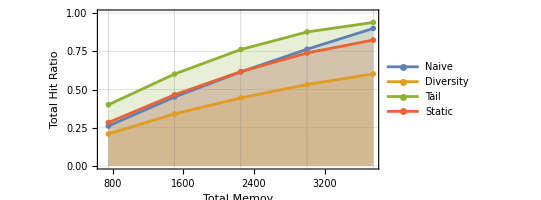

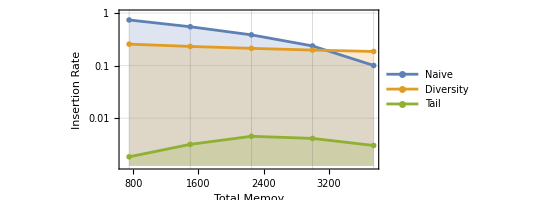

```mathematica
xAxes = {250,500,750,1000,1250};
ListLinePlot[dataHitRatio2,PlotMarkers->"OpenMarkers",GridLines->{3*xAxes,Automatic},Ticks->{xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memoy","Total Hit Ratio"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}},PlotLegends->{"Naive","Diversity","Tail","Static"},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"]]

ListLogPlot[dataInsertionRate2,PlotMarkers->"OpenMarkers",GridLines->{3*xAxes,Automatic},Filling->Axis,FrameLabel->{"Total Memoy","Insertion Rate"} ,Frame->True,AspectRatio->aspectRatio,PlotRange->{All,{0,1}},PlotLegends->{"Naive","Diversity","Tail"},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],Joined->True]
```